```mathematica
data={{1,0.0312},{2,0.0624},{3,0.2180401},{4,0.452403},{5,0.858005},{10,6.786043},{15,24.616958},{20,63.742009},{25,130.073634},{30,237.168320}}
```

{{1,0.0312},{2,0.0624},{3,0.21804},{4,0.452403},{5,0.858005},{10,6.78604},{15,24.617},{20,63.742},{25,130.074},{30,237.168}}

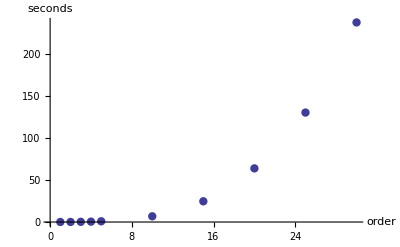

```mathematica
ListPlot[data,PlotStyle->PointSize[0.015],AxesLabel->{"order","seconds"}]
```

```mathematica
nlm=NonlinearModelFit[data,a +b ⅇ^(c x),{a,b,c},x]
```

FittedModel[-10.2471+6.39351 ⅇ^(«20» x)]

```mathematica
Normal[nlm]
```

-10.2471+6.39351 ⅇ^(0.122103 x)

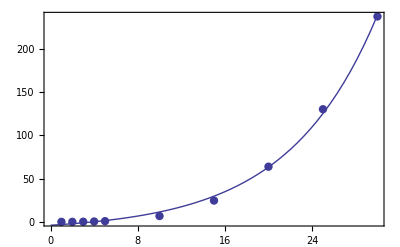

```mathematica
Show[ListPlot[data,PlotStyle->PointSize[0.015]],Plot[nlm[x],{x,0,30}],Frame->True]
```